# Examen parcial 3

## Ejercicio 1

a) La ecuación  puede escribirse como el sistema


Sus soluciones de equilibrio son  y , por lo que sólo existe para .
b) Calculamos los eigenvalores con la matriz Jacobiana:

```mathematica
J1={{D[y,x],D[y,y]},{D[a-Exp[x],x],D[a-Exp[x],y]}}
```

{{0,1},{-ⅇ^x,0}}

```mathematica
J1=J1/.{x->Log[a],y->0}
```

{{0,1},{-a,0}}

```mathematica
FullSimplify[Eigenvalues[J1]]
```

{-ⅈ √a,ⅈ √a}

Los eigenvalores son puramente reales. Sin embargo, recordemos que si la parte real de los eigenvalores es cero, no podemos decir nada acerca del punto de equilibrio, a menos de que el sistema sea conservativo o reversible. En este caso, el sistema es conservativo y reversible dado que la ecuación puede escribirse como el sistema mecánico  (por lo que es conservativo), y porque el lado derecho de la primera igualdad es impar en  y el lado derecho de la segunda igualdad es par en . Por lo tanto el punto de equilibrio es un centro verdadero del sistema no lineal.
c) La gráfica del espacio fase es:

```mathematica
Manipulate[StreamPlot[{y,a-Exp[x]},{x,-5,5},{y,-5,5},FrameLabel->{x,y}],{a,-2,2}]
```

## Ejercicio 2

Sistema:


a) Gráfica de ceroclinas

```mathematica
Manipulate[Plot[{2*x,m+x^2},{x,0,2},PlotRange->{{0,2},{0,4}},AxesLabel->{x,y}],{m,0,2}]
```

Las ceroclinas son una parábola y una recta que se intersectan. Pueden haber cero, una o dos intersecciones que corresponden a cero, uno o dos puntos de equilibrio mientras  varía, por lo que ocurre una bifurcación de nodo-silla.
c) Primero encontramos los puntos de equilibrio

```mathematica
Solve[{0==y-2*x,0==μ+x^2-y},{x,y}]
```

{{x→1-√(1-μ),y→2 (1-√(1-μ))},{x→1+√(1-μ),y→2 (1+√(1-μ))}}

Vemos que los puntos de equilibrio son iguales cuando , y no existen cuando , por lo que la bifurcación ocurre en  en el punto . Calculamos la matriz Jacobiana y evaluamos en un punto de equilibrio:

```mathematica
J2={{D[y-2*x,x],D[y-2*x,y]},{D[m+x^2-y,x],D[m+x^2-y,y]}}
```

{{-2,1},{2 x,-1}}

```mathematica
J2=J2/.x->1-√(1-μ)
```

{{-2,1},{2 (1-√(1-μ)),-1}}

```mathematica
Tr[J2]
```

-3

```mathematica
Det[J2]
```

2 √(1-μ)

Cuando , la traza es negativa y el determinante es positivo, por lo que la solución con signo negativo es el nodo estable, y la solución con signo positivo debe ser el punto silla. Finalmente, si nos fijamos en la forma de los puntos de equlibrio, vemos que tienen las normas  y . Graficamos estos valores tomando en cuenta que el nodo estable se grafica con una línea continua y el punto silla (inestable) se grafica con una línea punteada:

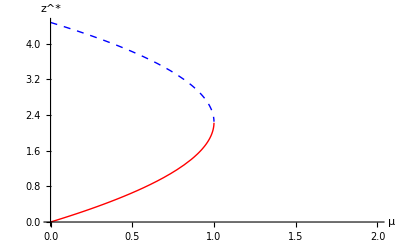

```mathematica
Show[{Plot[Sqrt[5]*(1-Sqrt[1-m]),{m,0,2},PlotStyle->{Red,Thick},AxesLabel->{μ,SuperStar[z]},PlotRange->{{0,2},{0,2*Sqrt[5]}}],Plot[Sqrt[5]*(1+Sqrt[1-m]),{m,0,2},PlotStyle->{Blue,Thick,Dashed}]}]
```

## Ejercicio 3

Si comparamos las ecuaciones 3 y 4 y las ecuaciones 6 y 7, vemos que son equivalentes con ,  y .
a) Calculamos la cantidad deseada:

```mathematica
f[x_,y_]:=x*y^2;
g[x_,y_]:=-x^2;
```

```mathematica
D[f[x,y],{x,3}]+D[f[x,y],{x,1},{y,2}]+D[g[x,y],{x,2},{y,1}]+D[g[x,y],{y,3}]+(D[f[x,y],{x,1},{y,1}]*(D[f[x,y],{x,2}]+D[f[x,y],{y,2}])-D[g[x,y],{x,1},{y,1}]*(D[g[x,y],{x,2}]+D[g[x,y],{y,2}])-D[f[x,y],{x,2}]*D[g[x,y],{x,2}]+D[f[x,y],{y,2}]*D[g[x,y],{y,2}])
```

2+4 x y

La cual, evaluada en  es .
b) Vemos que las ecuaciones 8 y 9 son exactamente las 6 y 7 con , por lo que si en  ocurre una bifurcación de Hopf, la cantidad calculada anteriormente, evaluada en el origen nos dice si la bifurcación es supercrítica, subcrítica  degenerada. En este caso es positiva por lo que debe ser subcrítica. Sólo debemos comprobar que, efectivamente, en el origen hay una bifurcación de Hopf cuando . Es obvio que el origen es un punto de equilibrio, dadas las ecuaciones. Sólo basta con encontrar los eigenvalores en el origen:

```mathematica
J3={{D[-y+m*x+x*y^2,x],D[-y+m*x+x*y^2,y]},{D[x+m*y-x^2,x],D[x+m*y-x^2,y]}}
```

{{m+y^2,-1+2 x y},{1-2 x,m}}

```mathematica
J3/.{x->0,y->0}
```

{{m,-1},{1,m}}

```mathematica
Eigenvalues[{{m,-1},{1,m}}]
```

{-ⅈ+m,ⅈ+m}

Comprobamos que cuando  es una espiral estable y cuando  es una espiral inestable, atravesando el eje imaginario cuando .

c) El ciclo límite es la frontera entre la solución que tiende al punto de equilibrio y la que se aleja del punto de equilibrio

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

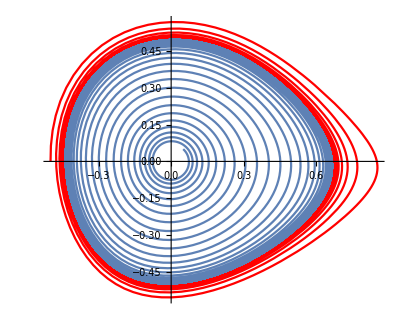

```mathematica
sol=NDSolve[{x'[t]==-y[t]-0.03*x[t]+x[t]*y[t]^2,y'[t]==x[t]-0.03*y[t]-x[t]^2,x[500]==0.05,y[500]==0.05},{x,y},{t,0,500}]
sol2=NDSolve[{x'[t]==-y[t]-0.03*x[t]+x[t]*y[t]^2,y'[t]==x[t]-0.03*y[t]-x[t]^2,x[500]==-0.5,y[500]==0},{x,y},{t,0,500}]
Show[{ParametricPlot[Evaluate[{x[t],y[t]}/.sol2],{t,0,500},PlotPoints->100,PlotStyle->Red],ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,500},PlotPoints->100]}]
```

De forma más prolija:

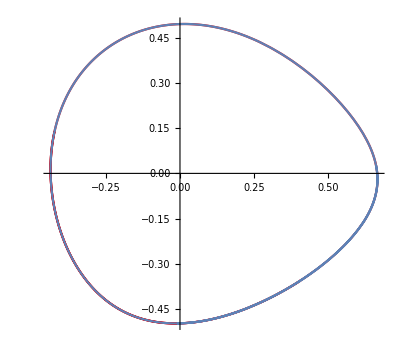

```mathematica
Show[{ParametricPlot[Evaluate[{x[t],y[t]}/.sol2],{t,0,10},PlotPoints->100,PlotStyle->Red],ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,10},PlotPoints->100]}]
```

## Ejercicio 4

Tenemos que ver el espacio fase cerca del origen, y podemos usar el teorema de la bisección para aproximar el punto en el cual pasamos de tener soluciones oscilatorias para todo tiempo a soluciones que divergen en tiempo finito. El punto crítico está aproximadamente en .

```mathematica
Manipulate[StreamPlot[{m*x+y-x^2,-x+m*y+2*x^2},{x,-1,1},{y,-1,1}],{m,0,0.1}]
```

```mathematica
sol=NDSolve[{x'[t]==0.08*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+0.08*y[t]+2*x[t]^2,x[0]==0.001,y[0]==-0.001},{x,y},{t,0,100}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

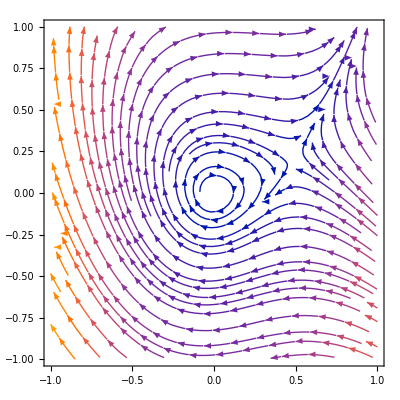

```mathematica
Show[StreamPlot[{0.08*x+y-x^2,-x+0.08*y+2*x^2},{x,-1,1},{y,-1,1}],ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,100},PlotStyle->Red]]
```

```mathematica
sol1=NDSolve[{x'[t]==0.036*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+0.036*y[t]+2*x[t]^2,x[0]==0.001,y[0]==-0.001},{x,y},{t,0,500}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

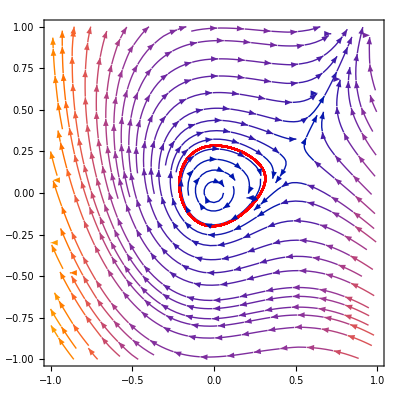

```mathematica
Show[StreamPlot[{0.036*x+y-x^2,-x+0.036*y+2*x^2},{x,-1,1},{y,-1,1}],ParametricPlot[Evaluate[{x[t],y[t]}/.sol1],{t,400,500},PlotStyle->Red]]
```

```mathematica
sol2=NDSolve[{x'[t]==0.0665*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+0.0665*y[t]+2*x[t]^2,x[0]==0.001,y[0]==-0.001},{x,y},{t,0,500}]
```

NDSolve::nderr: Error test failure at t == 144.209; unable to continue.

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

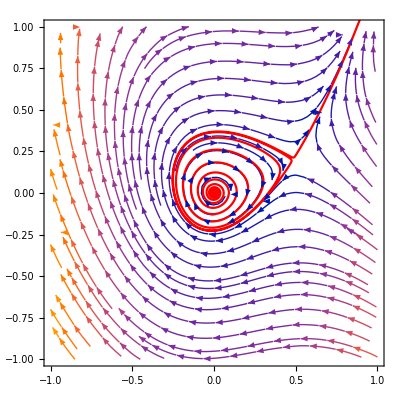

```mathematica
Show[StreamPlot[{0.0665*x+y-x^2,-x+0.0665*y+2*x^2},{x,-1,1},{y,-1,1}],ParametricPlot[Evaluate[{x[t],y[t]}/.sol2],{t,0,130},PlotStyle->Red]]
```

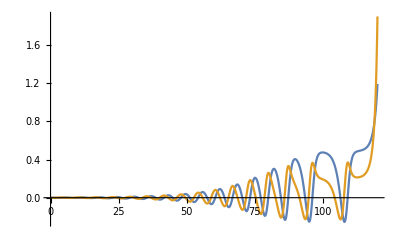

```mathematica
Plot[Evaluate[{x[t],y[t]}/.sol2],{t,0,120},PlotRange->All]
```

```mathematica
Solve[{0.0665*x+y-x^2==0,-x+0.0665*y+2*x^2==0},{x,y}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0.,y→0.},{x→0.48605,y→0.203922}}

```mathematica
jak=({{D[0.0665*x+y-x^2,x], D[0.0665*x+y-x^2,y]}, {D[-x+0.0665*y+2*x^2,x], D[-x+0.0665*y+2*x^2,y]}})/.{x->0.4860499637067505,y->0.20392224463283462}
```

{{-0.9056,1},{0.9442,0.0665}}

```mathematica
Eigensystem[jak]
```

{{-1.50603,0.666933},{{-0.857329,0.514768},{-0.536607,-0.843832}}}

```mathematica
homc=NDSolve[{x'[t]==0.0665*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+0.0665*y[t]+2*x[t]^2,x[0]==0.4860499637067505-0.0005366071401137466,y[0]==0.20392224463283462-0.0008438321972874382},{x,y},{t,0,500}]
```

NDSolve::nderr: Error test failure at t == 48.5655; unable to continue.

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

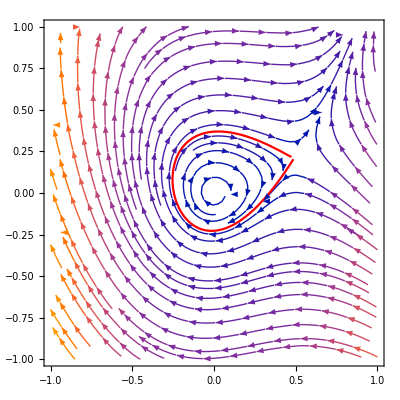

```mathematica
Show[StreamPlot[{0.0665*x+y-x^2,-x+0.0665*y+2*x^2},{x,-1,1},{y,-1,1}],ParametricPlot[Evaluate[{x[t],y[t]}/.homc],{t,0,16},PlotStyle->Red]]
```